```mathematica
(* Calculate the effective nonlinearities for random regular networks, as well as random regular networks with global inhibition
```

```mathematica
(* The eigenvalue distribution is calculated for each value of J, so be sure not to mix up evaluation of cells for different values of J.
```

```mathematica
(* Eigenvalue threshold, parametrized in terms of k \in [0,1]
```

```mathematica
Λk[k_,Λmax_,Λmin_] := ((Λmax-Λmin)*k+Λmin)
```

```mathematica
NIntegrate[((2*3)/Pi Sqrt[4*J0^2*(3-1)-(x+J0)^2]/(3^2*4*J0^2-4*(x+J0)^2)),{x,- J0*(2*Sqrt[2]+1),J0*(2*Sqrt[2]-1)}]
```

1.

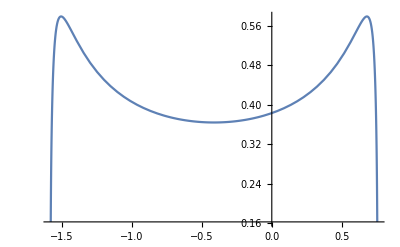

```mathematica
Plot[((2*3)/Pi Sqrt[4*J0^2*(3-1)-(x+J0)^2]/(3^2*4*J0^2-4*(x+J0)^2)),{x,- J0*(2*Sqrt[2]+1),J0*(2*Sqrt[2]-1)}]
```

```mathematica
(* =================== *)
```

```mathematica
(* J0 = 1.085 (Jc/2)
```

```mathematica
(* =================== *)
```

```mathematica
deg = 3;
```

```mathematica
J0 =1.085;
```

```mathematica
Λmax = J0*(2*Sqrt[deg-1]-1);
```

```mathematica
Λmin = - J0*(2*Sqrt[deg-1]+1);
```

```mathematica
PhisolnO4absorbingrandreg[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{500}}}}]
```

```mathematica
PhiO4lattd3J1p085 = PhisolnO4absorbingrandreg[0,40,-0.5]
```

{{Φ1→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ2→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ3→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ4→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>]}}

```mathematica
Evaluate[Φ1[1,1]/.PhiO4lattd3J1p085]
```

{0.188484-2.91673×10^-12 ⅈ}

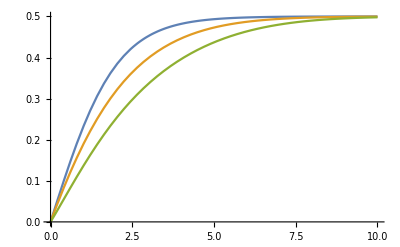

```mathematica
Plot[{LogisticSigmoid[y]-0.5,Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J1p085],Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J1p085]},{y,0,10}]
```

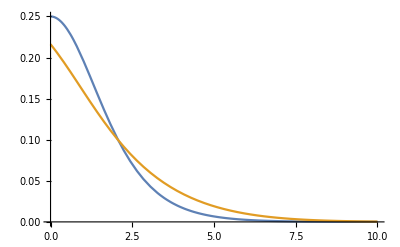

```mathematica
Plot[{LogisticSigmoid'[y],Re[Derivative[0,1][Φ1][1,y]]/.PhiO4lattd3J1p085},{y,0,10}]
```

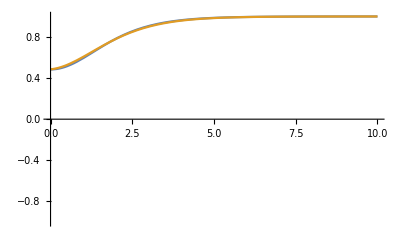

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J1p085},{y,0,10},PlotRange->{-1,1}]
```

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J1p085},{y,0,10}],{k,0,1}]
```

ReplaceAll::reps: {PhiO4lattd3J0p83} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
PhiO4lattJ1p085tbl = Table[{y,Last[Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J1p085]],Last[Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J1p085]],Last[Evaluate[Re[Φ3[1,y]]/.PhiO4lattd3J1p085]]},{y,0,10,0.05}];
```

```mathematica
Export["NPRGPhi_randreg_deg3_absorbingsigmoid_J1p085_O4.txt",PhiO4lattJ1p085tbl,"Table"];
```

```mathematica
(* =================== *)
```

```mathematica
(* J0 = 1.16 (Jc/2 for rr with inhib)
```

```mathematica
(* =================== *)
```

```mathematica
deg = 3;
```

```mathematica
J0 =1.16;
```

```mathematica
Λmax = J0*(2*Sqrt[deg-1]-1);
```

```mathematica
Λmin = - J0*(2*Sqrt[deg-1]+1);
```

```mathematica
PhisolnO4absorbingrandreg[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{500}}}}]
```

```mathematica
PhiO4lattd3J1p16 = PhisolnO4absorbingrandreg[0,40,-0.5]
```

{{Φ1→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ2→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ3→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ4→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>]}}

```mathematica
Evaluate[Φ1[1,1]/.PhiO4lattd3J1p16]
```

{0.188484-2.91673×10^-12 ⅈ}

```mathematica
Plot[{LogisticSigmoid[y]-0.5,Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J1p16],Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J1p16]},{y,0,10}]
```

-Graphics-

```mathematica
Plot[{LogisticSigmoid'[y],Re[Derivative[0,1][Φ1][1,y]]/.PhiO4lattd3J1p16},{y,0,10}]
```

-Graphics-

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J1p16},{y,0,10},PlotRange->{-1,1}]
```

-Graphics-

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J1p16},{y,0,10}],{k,0,1}]
```

```mathematica
PhiO4lattJ1p16tbl = Table[{y,Last[Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J1p16]],Last[Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J1p16]],Last[Evaluate[Re[Φ3[1,y]]/.PhiO4lattd3J1p16]]},{y,0,10,0.05}];
```

```mathematica
Export["NPRGPhi_randreg_deg3_absorbingsigmoid_J1p16_O4.txt",PhiO4lattJ1p16tbl,"Table"];
```

```mathematica
(* =================== *)
```

```mathematica
(* J0 = 2.17 (Jc)
```

```mathematica
(* =================== *)
```

```mathematica
deg = 3;
```

```mathematica
J0 =2.17;
```

```mathematica
Λmax = J0*(2*Sqrt[deg-1]-1);
```

```mathematica
Λmin = - J0*(2*Sqrt[deg-1]+1);
```

```mathematica
PhisolnO4absorbingrandreg[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{500}}}}]
```

```mathematica
PhiO4lattd3J2p17 = PhisolnO4absorbingrandreg[0,40,-0.5]
```

{{Φ1→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ2→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ3→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ4→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>]}}

```mathematica
Evaluate[Φ1[1,1]/.PhiO4lattd3J2p17]
```

{0.188484-2.91673×10^-12 ⅈ}

```mathematica
Plot[{LogisticSigmoid[y]-0.5,Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J2p17],Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J2p17]},{y,0,10}]
```

-Graphics-

```mathematica
Plot[{LogisticSigmoid'[y],Re[Derivative[0,1][Φ1][1,y]]/.PhiO4lattd3J2p17},{y,0,10}]
```

-Graphics-

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J2p17},{y,0,10},PlotRange->{-1,1}]
```

-Graphics-

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J2p17},{y,0,10}],{k,0,1}]
```

```mathematica
PhiO4lattJ2p17tbl = Table[{y,Last[Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J2p17]],Last[Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J2p17]],Last[Evaluate[Re[Φ3[1,y]]/.PhiO4lattd3J2p17]]},{y,0,10,0.05}];
```

```mathematica
Export["NPRGPhi_randreg_deg3_absorbingsigmoid_J2p17_O4.txt",PhiO4lattJ2p17tbl,"Table"];
```

```mathematica
(* =================== *)
```

```mathematica
(* J0 = 2.32 (Jc for rr with inhib)
```

```mathematica
(* =================== *)
```

```mathematica
deg = 3;
```

```mathematica
J0 =2.32;
```

```mathematica
Λmax = J0*(2*Sqrt[deg-1]-1);
```

```mathematica
Λmin = - J0*(2*Sqrt[deg-1]+1);
```

```mathematica
PhisolnO4absorbingrandreg[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{500}}}}]
```

```mathematica
PhiO4lattd3J2p32 = PhisolnO4absorbingrandreg[0,40,-0.5]
```

{{Φ1→InterpolatingFunction[…],Φ2→InterpolatingFunction[…],Φ3→InterpolatingFunction[…],Φ4→InterpolatingFunction[…]}}

```mathematica
Evaluate[Φ1[1,1]/.PhiO4lattd3J2p32]
```

{0.18444}

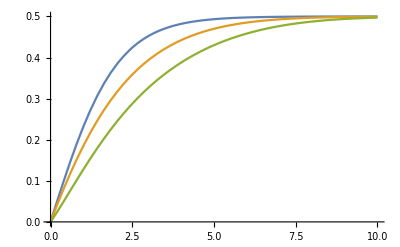

```mathematica
Plot[{LogisticSigmoid[y]-0.5,Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J2p32],Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J2p32]},{y,0,10}]
```

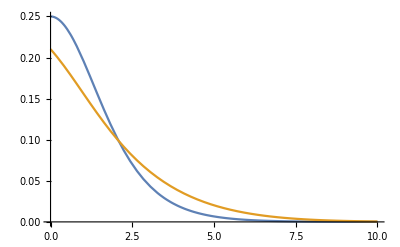

```mathematica
Plot[{LogisticSigmoid'[y],Re[Derivative[0,1][Φ1][1,y]]/.PhiO4lattd3J2p32},{y,0,10}]
```

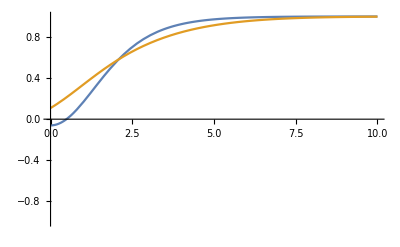

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J2p32},{y,0,10},PlotRange->{-1,1}]
```

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J2p32},{y,0,10}],{k,0,1}]
```

```mathematica
PhiO4lattJ2p32tbl = Table[{y,Last[Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J2p32]],Last[Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J2p32]],Last[Evaluate[Re[Φ3[1,y]]/.PhiO4lattd3J2p32]]},{y,0,10,0.05}];
```

```mathematica
Export["NPRGPhi_randreg_deg3_absorbingsigmoid_J2p32_O4.txt",PhiO4lattJ2p32tbl,"Table"];
```

```mathematica
(* =================== *)
(* J0 = 4.34 (2*Jc)
(* =================== *)
```

```mathematica
deg = 3;
```

```mathematica
J0 =4.34;
```

```mathematica
Λmax = J0*(2*Sqrt[deg-1]-1);
```

```mathematica
Λmin = - J0*(2*Sqrt[deg-1]+1);
```

```mathematica
PhisolnO4absorbingrandreg[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{2000}}}}]
```

```mathematica
PhiO4lattd3J4p34 = PhisolnO4absorbingrandreg[0,40,-0.5]
```

NDSolve::ndsz: At k == 1., step size is effectively zero; singularity or stiff system suspected.

{{Φ1→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ2→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ3→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ4→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>]}}

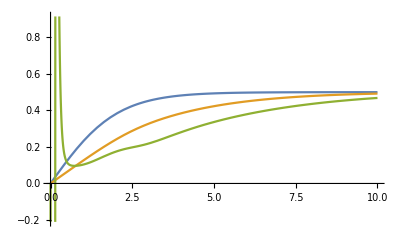

```mathematica
Plot[{LogisticSigmoid[y]-0.5,Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J4p34],Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J4p34]},{y,0,10}]
```

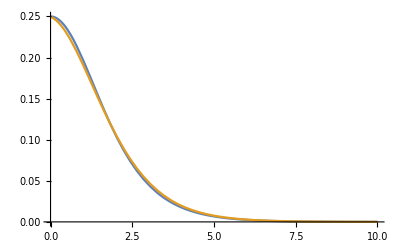

```mathematica
Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J4p34},{y,0,10}]
```

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J4p34},{y,0,10},PlotRange->{-1,1}]
```

-Graphics-

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J4p34},{y,0,10}],{k,0,1}]
```

```mathematica
PhiO4lattJ4p34tbl = Table[{y,Last[Evaluate[Re[Φ1[ 1,y]]/.PhiO4lattd3J4p34]],Last[Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J4p34]],Last[Evaluate[Re[Φ3[ 1,y]]/.PhiO4lattd3J4p34]]},{y,0,10,0.05}];
```

```mathematica
Export["NPRGPhi_randreg_deg3_absorbingsigmoid_J4p34_O4.txt",PhiO4lattJ4p34tbl,"Table"];
```

```mathematica
(* =================== *)
```

```mathematica
(* J0 = 4.64 (2*Jc for rr with inhib)
```

```mathematica
(* =================== *)
```

```mathematica
deg = 3;
```

```mathematica
J0 =4.64;
```

```mathematica
Λmax = J0*(2*Sqrt[deg-1]-1);
```

```mathematica
Λmin = - J0*(2*Sqrt[deg-1]+1);
```

```mathematica
PhisolnO4absorbingrandreg[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*Re[((2*deg)/Pi Sqrt[4*J0^2*(deg-1)-(Λk[k,Λmax,Λmin]+J0)^2]/(deg^2*4*J0^2-4*(Λk[k,Λmax,Λmin]+J0)^2))]*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{1000}}}}]
```

```mathematica
PhiO4lattd3J4p64 = PhisolnO4absorbingrandreg[0,40,-0.5]
```

{{Φ1→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ2→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ3→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>],Φ4→InterpolatingFunction[{{0., 1.}, {0., 40.}}, <>]}}

```mathematica
Evaluate[Φ1[1,1]/.PhiO4lattd3J4p64]
```

{0.117465}

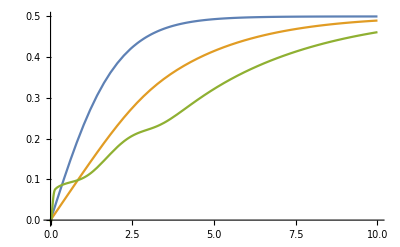

```mathematica
Plot[{LogisticSigmoid[y]-0.5,Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J4p64],Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J4p64]},{y,0,10}]
```

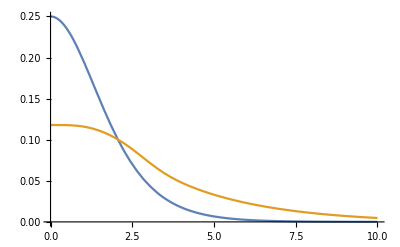

```mathematica
Plot[{LogisticSigmoid'[y],Re[Derivative[0,1][Φ1][1,y]]/.PhiO4lattd3J4p64},{y,0,10}]
```

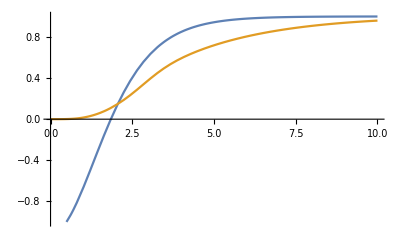

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J4p64},{y,0,10},PlotRange->{-1,1}]
```

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J4p64},{y,0,10}],{k,0,1}]
```

```mathematica
PhiO4lattJ4p64tbl = Table[{y,Last[Evaluate[Re[Φ1[1,y]]/.PhiO4lattd3J4p64]],Last[Evaluate[Re[Φ2[1,y]]/.PhiO4lattd3J4p64]],Last[Evaluate[Re[Φ3[1,y]]/.PhiO4lattd3J4p64]]},{y,0,10,0.05}];
```

```mathematica
Export["NPRGPhi_randreg_deg3_absorbingsigmoid_J4p64_O4.txt",PhiO4lattJ4p64tbl,"Table"];
```